### GB/T 4548玻璃瓶罐内表面耐水性标准中 表2分类等级研究（马斌）

#### -Graphics--Graphics- GB/T 4548标准中表2分类等级数据{体积v1，耗酸v2}

```mathematica
(*GB/T 4548-1995 耐水性分级原始数据*)
data1={{1,20.0},{2,17.6},{5,13.2},{10,10.2},{20,8.1},{50,6.1},{100,4.8},{200,3.8},{500,2.9}};
```

#### mathematica的非线性函数拟合公式

```mathematica
fit=NonlinearModelFit[data1,a*x^(-b),{a,b},x]
fit["BestFitParameters"]
(*输出:{a->值,b->值}*)

(*拟合函数表达式*)
fit[x]
(*输出:20.9702/x^0.300287*)
```

FittedModel[…]

{a→20.77,b→0.308173}

20.77/x^0.308173

#### JMP软件中的拟合公式

```mathematica
Solve[Log[y]==3.05616-0.3210 Log[x],y]
```

{{y→21.2458/x^0.321}}

#### 合并mathematica和JMP软件拟合公式的图像（结论：两个拟合公式差异不大）

```mathematica
suang1=Plot[{21.246 x^-0.321,20.77 x^-0.308173},{x,0,600},PlotLabels->{"-0.321","-0.308"},PlotRange->{{0, 650}, {0, 22}}]
```

-Graphics-

#### 绘制GB/T 4548标准中表2分类等级数据的点图

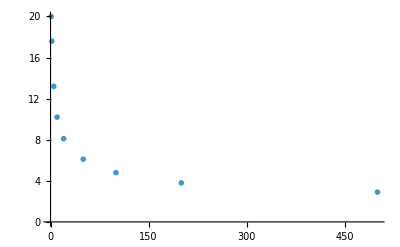

```mathematica
dian1=ListPlot[data1,PlotMarkers->"OpenMarkers"]
```

#### 合并三个图像（结论：两个拟合公式差异不大，JMP公式更优（从国际标准来衡量））

```mathematica
Show[suang1,dian1]
```

-Graphics-

### 玻璃瓶容量恒定下，细胖、圆扁形状与耐水性的关系

#### 结论1：体积固定时，半径越大 → 底面积越大 → 高度必须越小 （即矮胖）→ 侧壁面积越小 --→ 耐水性会相对好些。

```mathematica
Manipulate[h=V/(Pi r^2);
sideArea=2 Pi r h;
Column[{Plot[2 V/x,{x,0.3,3},AxesLabel->{"半径 r","侧面积"},PlotLabel->Style["体积恒定 V = "<>ToString[V]<>"  当前侧面积 = "<>ToString[NumberForm[sideArea,{3,2}]],Bold],PlotRange->{0,10},Epilog->{PointSize[Large],Red,Point[{r,sideArea}],Dashed,Line[{{r,0},{r,sideArea}}]},ImageSize->400],Graphics3D[{Cylinder[{{0,0,0},{0,0,h}},r],Red,Thick,Text[Style["r = "<>ToString[NumberForm[r,{2,2}]]<>"  h = "<>ToString[NumberForm[h,{2,2}]],Red,FontSize->14],{r,0,h/2}]},Axes->True,AxesLabel->{"x","y","z"},Boxed->True,ImageSize->300,ViewPoint->{2,-2,1}]},Alignment->Center],{{V,1,"体积 V"},0.5,4,Appearance->"Labeled"},{{r,0.8,"半径 r"},0.4,2.5,Appearance->"Labeled"},TrackedSymbols:>{V,r}]
```

#### 结论2：体积固定时，由椭圆越趋向圆形→ 侧壁面积越小--→ 耐水性会相对好些。

```mathematica
(*清除环境*)ClearAll["Global`*"]

(*固定体积*)
V0=1;

(*椭圆柱侧面积函数*)
Sellipse[a_,b_]:=Module[{perimeter,height},(*椭圆周长近似公式（高精度）*)perimeter=4 a EllipticE[1-(b/a)^2];
height=V0/(Pi a b);
perimeter*height];

(*圆柱侧面积函数（底面积相等）*)
SCylinder[a_,b_]:=Module[{r,height},r=Sqrt[a b];(*等底面积条件*)height=V0/(Pi a b);
2 Pi r*height];

(*动态演示*)
Manipulate[(*计算实时参数*)rCyl=Sqrt[a b];
hVal=V0/(Pi a b);
Sell=Sellipse[a,b];
Scyl=SCylinder[a,b];
ratio=Sell/Scyl;
(*确保高度有效*)If[hVal<=0.01,hVal=0.01];
(*主界面布局*)Grid[{(*第一行：图表对比*){Panel[Grid[{{Style["椭圆柱体 vs 圆柱体 侧面积比较",Bold,16],SpanFromLeft},{},{(*左侧：侧面积曲线*)Plot[{Sellipse[x,b],SCylinder[x,b]},{x,0.5,3},AxesLabel->{"半长轴 a","侧面积 S"},PlotLabel->Style["固定体积 V = "<>ToString[V0],Bold,10],PlotRange->{0,12},PlotStyle->{{Blue,Thick},{Red,Thick}},PlotLegends->Placed[{"椭圆柱","圆柱"},Top],Epilog->{{Blue,PointSize[Large],Point[{a,Sell}]},{Red,PointSize[Large],Point[{a,Scyl}]},{Dashed,Gray,Line[{{a,0},{a,Sell}}],Line[{{a,0},{a,Scyl}}]}},GridLines->Automatic,ImageSize->350],(*右侧：面积比曲线*)Plot[Sellipse[x,b]/SCylinder[x,b],{x,0.5,3},AxesLabel->{"半长轴 a","面积比 S_ell/S_cyl"},PlotLabel->"比值 = "<>ToString[NumberForm[ratio,{3,2}]],PlotRange->{0.5,3},PlotStyle->{Purple,Thick},Epilog->{{Purple,PointSize[Large],Point[{a,ratio}]},{Dashed,Gray,Line[{{a,0},{a,ratio}}]},{Brown,Dashed,Line[{{0.5,1},{3,1}}]},{Text[Style["圆柱更优 (比值=1)",Bold,10,Brown],{2.5,1.05}]}},GridLines->Automatic,ImageSize->350]}}],SpanFromLeft]},(*第二行：三维模型对比*){Panel[Style["三维模型对比（可拖拽旋转视角）",Bold,12],Style["椭圆柱体",Blue,Bold,14],Style["圆柱体",Red,Bold,14]],SpanFromLeft},{(*椭圆柱体 3D*)Panel[ParametricPlot3D[{a Cos[u],b Sin[u],v},{u,0,2 Pi},{v,0,hVal},PlotStyle->Directive[Blue,Opacity[0.7],Specularity[White,30]],Mesh->{24,8},MeshStyle->{Gray,Gray},BoundaryStyle->Directive[Blue,Thick],Axes->True,AxesLabel->{"X","Y","Z"},Boxed->True,BoxRatios->{Automatic,Automatic,0.5},PlotLabel->Style["椭圆柱体\n半长轴 a = "<>ToString[NumberForm[a,{2,2}]]<>"  半短轴 b = "<>ToString[NumberForm[b,{2,2}]]<>"\n"<>"侧面积 S = "<>ToString[NumberForm[Sell,{3,2}]],Blue,Bold,12],ImageSize->300,ViewPoint->{1.8,-2.2,1.5},Lighting->"Neutral",Background->White],Alignment->Center],(*圆柱体 3D*)Panel[ParametricPlot3D[{rCyl Cos[u],rCyl Sin[u],v},{u,0,2 Pi},{v,0,hVal},PlotStyle->Directive[Red,Opacity[0.7],Specularity[White,30]],Mesh->{24,8},MeshStyle->{Gray,Gray},BoundaryStyle->Directive[Red,Thick],Axes->True,AxesLabel->{"X","Y","Z"},Boxed->True,BoxRatios->{Automatic,Automatic,0.5},PlotLabel->Style["圆柱体\n半径 r = "<>ToString[NumberForm[rCyl,{2,2}]]<>"  高 h = "<>ToString[NumberForm[hVal,{2,2}]]<>"\n"<>"侧面积 S = "<>ToString[NumberForm[Scyl,{3,2}]],Red,Bold,12],ImageSize->300,ViewPoint->{1.8,-2.2,1.5},Lighting->"Neutral",Background->White],Alignment->Center]}},Spacings->{2,2}],(*控制面板*){{a,1.5,"椭圆柱半长轴 a"},0.6,3,0.01,Appearance->"Labeled"},{{b,0.8,"椭圆柱半短轴 b"},0.4,2,0.01,Appearance->"Labeled"},(*同步参数提示*)ControlPlacement->Bottom,TrackedSymbols:>{a,b},Initialization:>((*预定义椭圆周长函数*)EllipsePerimeter[a_,b_]:=4 a EllipticE[1-(b/a)^2];)]
```